```mathematica
Clear[f,r]
a=(4 πGm^2)/kT;
f=2/(a*r^2)

FullSimplify[D[f,r]]
FullSimplify[-a*f*Integrate[f*r^2,{r,0,r}]/r^2]
```

kT/(2 r^2 πGm^2)

-kT/(r^3 πGm^2)

-kT/(r^3 πGm^2)

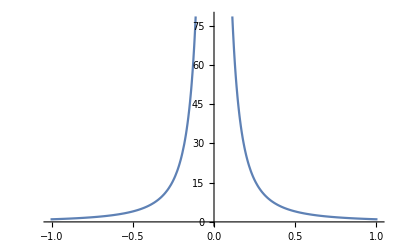

```mathematica
Plot[1/r^2,{r,-1.0069314718055995,1.0069314718055995}]
```

```mathematica
Manipulate[Plot[f,{r,-1.0069314718055995,1.0069314718055995}],{kT,-1.,1.},{πGm,-2,2}]
```